```mathematica
usbcs = {"adcirc_flow", "adcirc_stage", "rdhm_flow"};
dsbcs = {"adcirc_stage", "stage_0", "noriver_adcirc_stage"};
sites = {"greenville", "rock_springs", "grimesland"};
```

```mathematica
Quiet[



s2=Show[
 hecplot["Floyd", "rdhm_flow", "adcirc_stage", "greenville", "flow", 
  False, Blue],
 hecplot["Floyd", "rdhm_flow", "noriver_adcirc_stage", "greenville", 
  "flow", False, Blue],
 hecplot["Floyd", "rivers_on", "fine_grid", "greenville", "flow", 
  True, Green],
 hecplot["Floyd", "adcirc_stage", "adcirc_stage", "greenville", 
  "flow", False, Red],
 hecplot["Floyd", "adcirc_stage", "noriver_adcirc_stage", 
  "greenville", "flow", False, Red],
 hecplot["Floyd", "rivers_on", "fine_grid", "greenville", "flow", 
  True, Green]];


s4=Show[
 hecplot["Floyd", "rdhm_flow", "adcirc_stage", "tarboro", 
  "flow", False, Blue],
 hecplot["Floyd", "rdhm_flow", "noriver_adcirc_stage", "tarboro",
   "flow", False, Blue],
 hecplot["Floyd", "rivers_on", "fine_grid", "tarboro", "flow", 
  True, Green],
 hecplot["Floyd", "adcirc_stage", "adcirc_stage", "tarboro", 
  "flow", False, Red],
 hecplot["Floyd", "adcirc_stage", "noriver_adcirc_stage", 
  "tarboro", "flow", False, Red],
 hecplot["Floyd", "rivers_on", "fine_grid", "tarboro", "flow", 
  True, Green]];
```

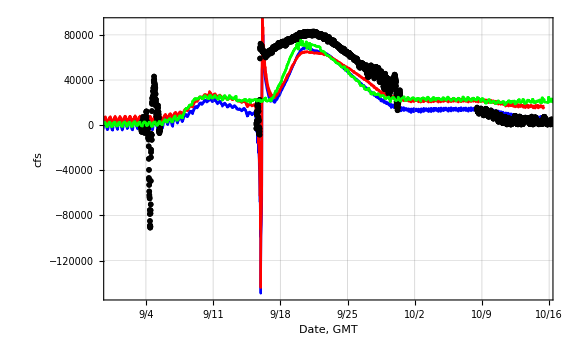

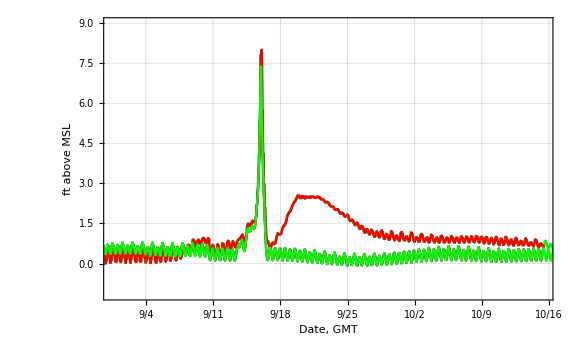

```mathematica
Quiet[
s5=Show[
 hecplot["Floyd", "rdhm_flow", "adcirc_stage", "washington", 
  "flow", False, Blue],
 hecplot["Floyd", "rdhm_flow", "noriver_adcirc_stage", "washington",
   "flow", False, Blue],
 hecplot["Floyd", "rivers_on", "fine_grid", "washington", "flow", 
  True, Green],
 hecplot["Floyd", "adcirc_stage", "adcirc_stage", "washington", 
  "flow", False, Red],
 hecplot["Floyd", "adcirc_stage", "noriver_adcirc_stage", 
  "washington", "flow", False, Red],
 hecplot["Floyd", "rivers_on", "fine_grid", "washington", "flow", 
  True, Green]];

Quiet[
s6=Show[
 hecplot["Floyd", "rdhm_flow", "adcirc_stage", "washington", 
  "stage", False, Blue],
 hecplot["Floyd", "rdhm_flow", "noriver_adcirc_stage", "washington",
 "stage", False, Blue],
 hecplot["Floyd", "rivers_on", "fine_grid", "washington", "stage", 
  False, Green],
 hecplot["Floyd", "adcirc_stage", "adcirc_stage", "washington", 
  "stage", False, Red],
 hecplot["Floyd", "adcirc_stage", "noriver_adcirc_stage", 
  "washington", "stage", False, Red],
 hecplot["Floyd", "rivers_off", "coarse_grid", "washington","stage", 
 False, Green]];



]
]
s5
s6
```

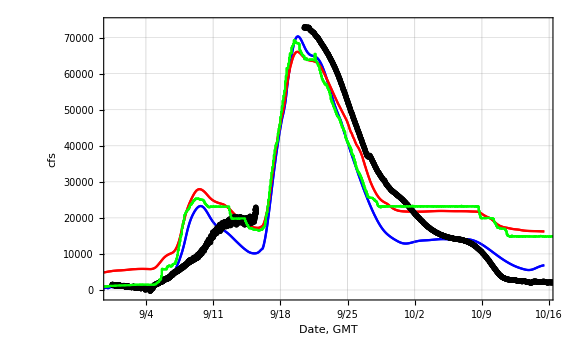

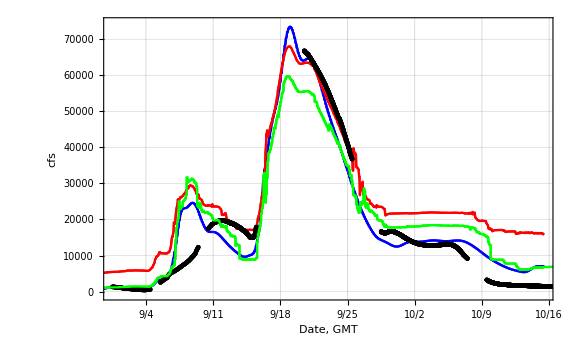

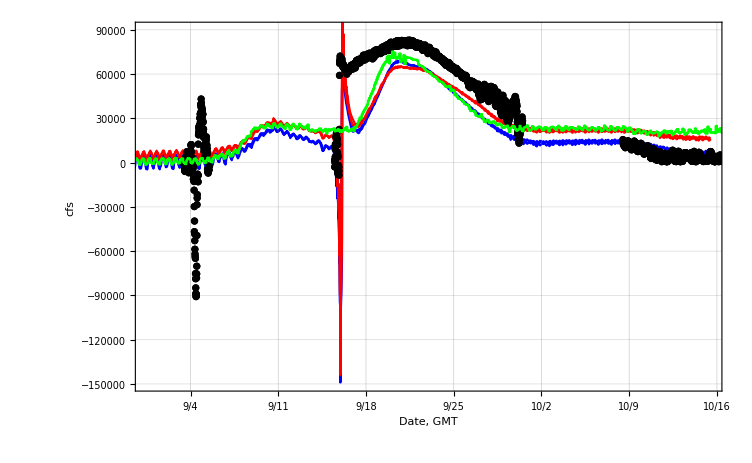

```mathematica
s2

s4
s5
```

```mathematica
s5=Show[
 hecplot["Floyd", "rdhm_flow", "adcirc_stage", "washington", 
  "flow", False, Blue],
 hecplot["Floyd", "rdhm_flow", "noriver_adcirc_stage", "washington",
   "flow", False, Purple],
 hecplot["Floyd", "rivers_on", "fine_grid", "washington", "flow", 
  True, Green],
 hecplot["Floyd", "adcirc_stage", "adcirc_stage", "washington", 
  "flow", False, Red],
 hecplot["Floyd", "adcirc_stage", "noriver_adcirc_stage", 
  "washington", "flow", False,Orange],
 hecplot["Floyd", "rivers_off", "coarse_grid", "washington", "flow", 
  True, Green]];
```

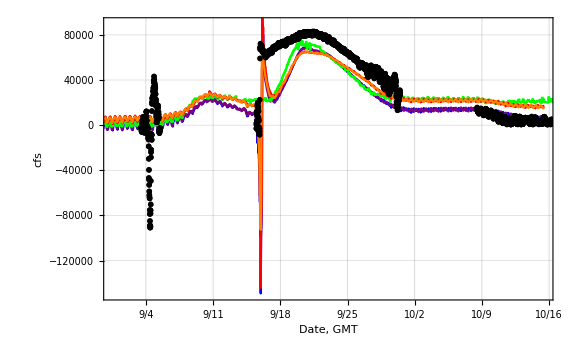

```mathematica
s5
```

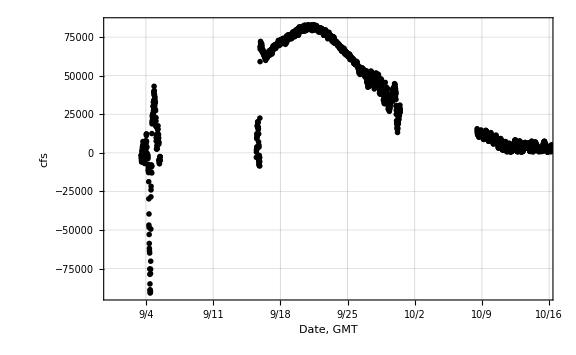

```mathematica
hecplot["Floyd", "rivers_off", "coarse_grid", "washington", "flow", 
  True, Green]
```

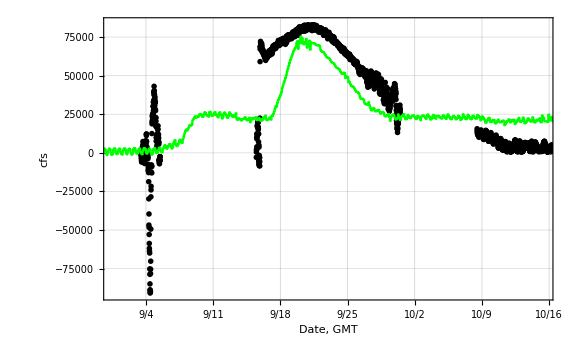

```mathematica
hecplot["Floyd", "rivers_on", "fine_grid", "washington", "flow", 
  True, Green]
```

```mathematica
s6=Show[
 hecplot["Floyd", "rdhm_flow", "adcirc_stage", "washington", 
  "stage",True, Blue],
 hecplot["Floyd", "rdhm_flow", "noriver_adcirc_stage", "washington",
 "stage", False, Blue],
 hecplot["Floyd", "rivers_on", "fine_grid", "washington", "stage", 
  False, Green],
 hecplot["Floyd", "adcirc_stage", "adcirc_stage", "washington", 
  "stage", False, Red],
 hecplot["Floyd", "adcirc_stage", "noriver_adcirc_stage", 
  "washington", "stage", False, Red],
 hecplot["Floyd", "rivers_off", "coarse_grid", "washington","stage", 
 False, Green]];
```

Thread::tdlen: Objects of unequal length in {"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {"0:00", "na", "-1530", "36404", "14.1", "1290", "36383", "18.586506", "0", "36383", "0", "0", "36383", "0", "0", "36383", "0", "na", "36327.29167", "na", "32.132818", "36390", "0.15", "1465.66", "36390", "0.21", "3045.72", "36390", "3.3", "3320.59", "36390", "5.29", "3296.89", "36390", "21", "5570.32", "36390", "0.15", "3477.98", "36390", "0.32", "3318.3", "36390", "3.35", "3317.7", "36390", "5.3", "3279.43", "36390", "17.01", « 106 »}\ « 1 » cannot be combined.

Thread::tdlen: Objects of unequal length in {"value", "36404.01", "na", "1460", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »}, « 49 », « 23377 »} cannot be transposed.

ToExpression::notstrbox: {"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: {"0:00", "na", "-1530", "36404", "14.1", "1290", "36383", "18.586506", "0", "36383", "0", "0", "36383", "0", "0", "36383", "0", "na", "36327.29167", "na", "32.132818", "36390", "0.15", "1465.66", "36390", "0.21", "3045.72", "36390", "3.3", "3320.59", "36390", "5.29", "3296.89", "36390", "21", "5570.32", "36390", "0.15", "3477.98", "36390", "0.32", "3318.3", "36390", "3.35", "3317.7", "36390", "5.3", "3279.43", "36390", "17.01", « 106 »}\ « 1 » is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: {"value", "36404.01", "na", "1460", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »}, « 49 », « 23377 »} cannot be transposed.

Part::partw: Part 2 of Transpose[{{"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »}, « 49 », « 23377 »}] does not exist.

Transpose::nmtx: The first two levels of {{"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »}, « 49 », « 23377 »} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Part::partw: Part 3 of Transpose[{{"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »}, « 49 », « 23377 »}] does not exist.

Part::partw: Part 2 of Transpose[{{"value", "36404", "na", "1500", "9/4/99"}\ {0, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 110 »}, « 49 », « 23377 »}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Delete::partw: Part 23427 of $Failed does not exist.

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

ListPlot::prng: Value of option PlotRange -> {{3145132800, 3149020800}, {-1 + Delete[$Failed, {{1}, {2}, {3}, {4807}, {4808}, {4809}, {4810}, {4811}, {4812}, {4813}, {4814}, {4815}, {4816}, {4817}, {4818}, {4819}, {4820}, {4821}, {4822}, {4823}, {4824}, {4825}, {4826}, {4827}, « 3 », {4831}, {4832}, {4833}, {4834}, {4835}, {4836}, {4837}, {4838}, {4839}, {4840}, {4841}, {4842}, {4843}, {4844}, {4845}, {4846}, {4847}, {4848}, {4849}, {4850}, {4851}, {4852}, {4853}, « 18574 »}], 1 + « 1 »}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

ListPlot::prng: Value of option PlotRange -> {{3145132800, 3149020800}, {-1 + Delete[$Failed, {{1}, {2}, {3}, {4807}, {4808}, {4809}, {4810}, {4811}, {4812}, {4813}, {4814}, {4815}, {4816}, {4817}, {4818}, {4819}, {4820}, {4821}, {4822}, {4823}, {4824}, {4825}, {4826}, {4827}, « 3 », {4831}, {4832}, {4833}, {4834}, {4835}, {4836}, {4837}, {4838}, {4839}, {4840}, {4841}, {4842}, {4843}, {4844}, {4845}, {4846}, {4847}, {4848}, {4849}, {4850}, {4851}, {4852}, {4853}, « 18574 »}], 1 + « 1 »}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{3145132800, 3149020800}, {-1 + Delete[$Failed, {{1}, {2}, {3}, {4807}, {4808}, {4809}, {4810}, {4811}, {4812}, {4813}, {4814}, {4815}, {4816}, {4817}, {4818}, {4819}, {4820}, {4821}, {4822}, {4823}, {4824}, {4825}, {4826}, {4827}, « 3 », {4831}, {4832}, {4833}, {4834}, {4835}, {4836}, {4837}, {4838}, {4839}, {4840}, {4841}, {4842}, {4843}, {4844}, {4845}, {4846}, {4847}, {4848}, {4849}, {4850}, {4851}, {4852}, {4853}, « 18574 »}], 1 + « 1 »}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ListPlot[$Failed, Joined → False, PlotRange → {{3145132800, 3149020800}, {-1 + Delete[$Failed, {« 18624 »}], 1 + Delete[$Failed, {« 18624 »}]}}, Frame → True, FrameTicks → {{Automatic, None}, {{« 1 »}, None}}, FrameLabel → {« 1 »}, GridLines → {{3145435200, 3146040000, 3146644800, 3147249600, 3147854400, 3148459200, 3149064000}, Automatic}, BaseStyle → {FontSize → 14, FontFamily → .

Delete::partw: Part 23427 of $Failed does not exist.

General::stop: Further output of Delete :: partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in « 1 », « 4 », ListPlot[$Failed, Joined → True, PlotRange → {{3145132800, 3149020800}, {-1 + Min[Delete[« 2 »], Delete[« 2 »]], Max[1 + Delete[« 2 »], 1 + Delete[« 2 »]]}}, Frame → True, FrameTicks → {{Automatic, None}, {{« 1 »}, None}}, « 10 » → « 1 », GridLines → {{3145435200, 3146040000, 3146644800, 3147249600, 3147854400, 3148459200, 3149064000}, Automatic}, BaseStyle → {FontSize → 14, FontFamily → .

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

```mathematica
s6
```

Show[Show[ListPlot[$Failed,Joined→False,6,ImageSize→Large,PlotStyle→-Graphics-],ListPlot[$Failed,Joined→True,6,ImageSize→Large,PlotStyle→-Graphics-]],ListPlot[$Failed,Joined→True,6,ImageSize→Large,PlotStyle→-Graphics-],1,1,ListPlot[$Failed,Joined→True,6,ImageSize→Large,PlotStyle→-Graphics-],ListPlot[$Failed,Joined→True,6,ImageSize→Large,PlotStyle→-Graphics-]]
 |  |  |  |